## 65.3 mA

```mathematica
files = FileNames["65.3mA-*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
fitdata = Table[Select[data[[i, 2]], #[[1]]≥ 0.0054 && #[[1]]≤0.013&], {i, 1, Length[data]}];
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
funcs = Normal[#]&/@ nlms;
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

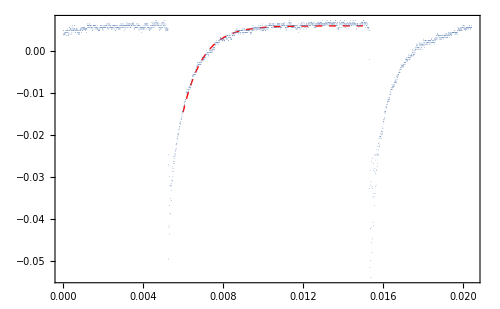
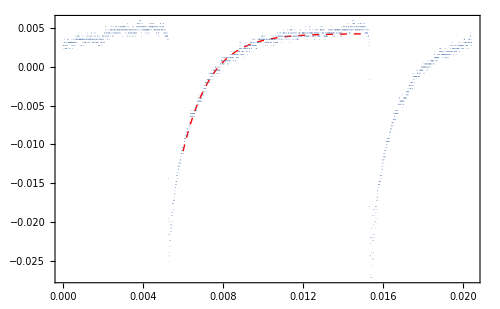
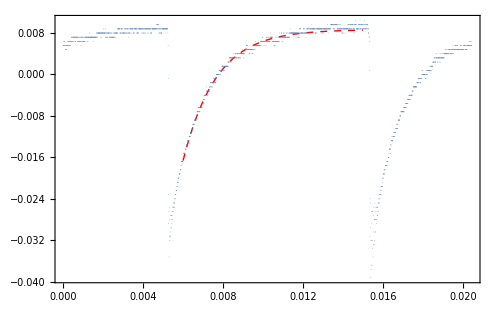
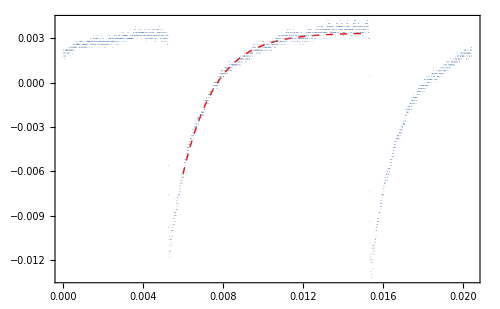
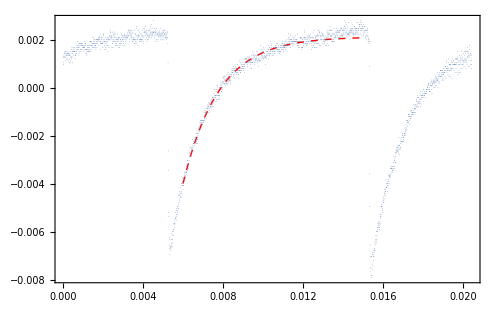
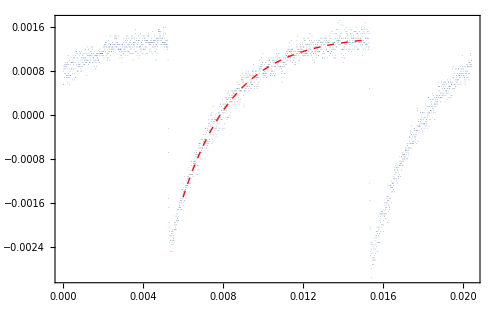
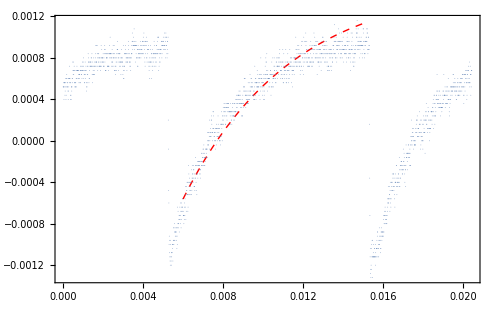
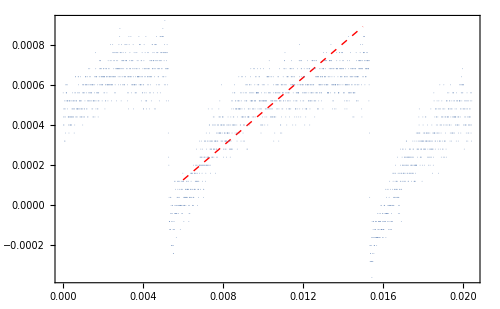

```mathematica
Show[Plot[#[[2]], {x, 0.006, 0.015},ImageSize->500, PlotRange->All, Frame->True, PlotStyle->{Red, Dashed, Thick}], ListPlot[#[[1, 2]],PlotStyle->{PointSize[0.00001]}]]&/@ Transpose[{data, funcs}]
```

{984.58,711.955,603.002,606.827,555.888,381.356,185.166,-0.37914}

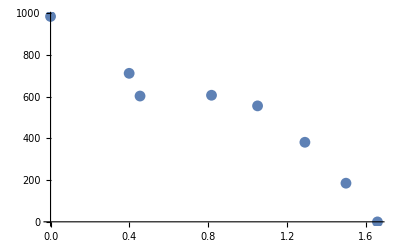

```mathematica
taus=#["ParameterTableEntries"][[3, 1]]&/@ nlms
filters = Drop[{0.,0.398736,0.453891,0.816374,1.04996,1.29003,1.49831,1.65801}, 0];
ListPlot[Transpose[{filters, taus}], PlotRange->All]
```

```mathematica
taudata = Transpose[{10^-filters, taus}]
```

{{1.,984.58},{0.399268,711.955},{0.351649,603.002},{0.152625,606.827},{0.0891333,555.888},{0.0512826,381.356},{0.0317461,185.166},{0.0219781,-0.37914}}

FittedModel[301.468+770.683 x]

3.3171

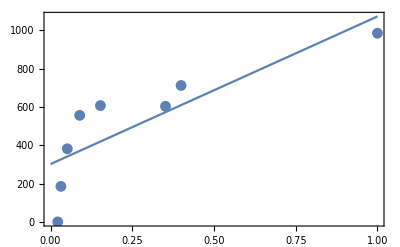

```mathematica
taufit = NonlinearModelFit[taudata, a + b x, {a, b}, x]
10^3/(taufit["ParameterTableEntries"][[1,1]])
Show[Plot[Normal[taufit], {x, 0, 1}, Frame->True, PlotRange->All], ListPlot[taudata]]
```